```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*INIITIALIZE PARAMETERS*)
(*------------------------------------------------------------------------------------------------------------------------------*)

alpha = 0.5;
beta = 1.0;
delta = 0.5;
katta =5;
qAvg = 1.0;
eta = 0.25;
etaBar = 0.5;
chi = 0.1;
uBar = 1.0;

(*------------------------------------------------------------------------------------------------------------------------------*)
(*AGENTS*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*Number of firms*)
n = 10.0;
(*A dummy vector used to identify each firm by a certain number: 1- first firm, 2-second firm,.....n- nth firm*)
Id = Table[i,{i,1,n}];
(*Number of consumers*)
m= 100.0;
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*PRICING*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*market share of the specialized firm*)
ms[t_,n_,q0_, qi_]:= q0 / Sum[qi[[t,i]],{i,1,n}];
(*markup smart components*)
etaSpec[delta_, etaSpecLag_, msSpec_, etaBar_]:=(1-delta)*etaSpecLag + delta*msSpec*etaBar;
(*price of specialist*)
pSpec[cs_,etaSpec_]:=(1+etaSpec)*cs;
(*price of firm if it produces the smart component*)
pFirmSelf[cSelf_,eta_]:=(1+eta)*cSelf;
(*price of firm if it produces the smart component*)
pFirmSpec[cSpec_,eta_]:=(1+eta)*cSpec;
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*MARGINAL COSTS*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*Marginal costs of the "usual" component*)
cp = 20.0;
(*Marginal costs of the smart component*)
cs = 10.0;
(*Marginal costs if firm buys smart component from specialist*)
cSelf[cp_, cs_]:=cp + cs
(*Marginal cost if firm buys smart component from specialist*)
cSpec[cp_,cs_, etaSpec_]:=cp + (1+etaSpec)*cs
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*PROFIT*)
(*------------------------------------------------------------------------------------------------------------------------------*)
profit[q_,p_,c_]:=q*p - c*q
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*QUALITY*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*quality of specialist*)
(*qualitySpec[t_,uBar_, alpha_, beta_,qAggSpec_] :=uBar*(1+ beta*qAggSpec^alpha)*)
(*quality of firm*)
qualityFirm[uBar_, alpha_, beta_,qFirm_ ] :=uBar*(1+ beta*qFirm^alpha)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*PROBABILITY*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*A function that computes the probability that consumer j buys from firm i*)
probability[i_,priceList_, qualityList_]:=Module[
{p =priceList, u = qualityList},
Exp[-chi*p[[i]]+ katta*u[[i]]]/Sum[Exp[-chi*p[[k]]+ katta*u[[k]]],{k,1,n}]]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------ EXERCISE 1 a) -------------------------------------------------------------*)
(*---------------------------------(*FIXED STRATEGIES: FIRMS PRODUCE SMART COMPONENT*)------------------------------------*)
```

Period Quantities: 15 | 7 | 9 | 8 | 9 | 12 | 6 | 14 | 11 | 9
57 | 0 | 1 | 0 | 2 | 7 | 0 | 30 | 3 | 0
100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

Prices: 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5

Qualities: 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
4.87298 | 3.64575 | 4. | 3.82843 | 4. | 4.4641 | 3.44949 | 4.74166 | 4.31662 | 4.
9.48528 | 3.64575 | 4.16228 | 3.82843 | 4.31662 | 5.3589 | 3.44949 | 7.63325 | 4.74166 | 4.
14.1149 | 3.64575 | 4.16228 | 3.82843 | 4.31662 | 5.3589 | 3.44949 | 7.63325 | 4.74166 | 4.
17.4924 | 3.64575 | 4.16228 | 3.82843 | 4.31662 | 5.3589 | 3.44949 | 7.63325 | 4.74166 | 4.

Agg. Quantities: 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
15. | 7. | 9. | 8. | 9. | 12. | 6. | 14. | 11. | 9.
72. | 7. | 10. | 8. | 11. | 19. | 6. | 44. | 14. | 9.
172. | 7. | 10. | 8. | 11. | 19. | 6. | 44. | 14. | 9.
272. | 7. | 10. | 8. | 11. | 19. | 6. | 44. | 14. | 9.

Profits: 112.5 | 52.5 | 67.5 | 60. | 67.5 | 90. | 45. | 105. | 82.5 | 67.5
427.5 | 0. | 7.5 | 0. | 15. | 52.5 | 0. | 225. | 22.5 | 0.
750. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
750. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
750. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

Probs: 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.569316 | 0.00123155 | 0.00723926 | 0.00306993 | 0.00723926 | 0.0737018 | 0.000461611 | 0.295245 | 0.0352563 | 0.00723926
0.999905 | 2.08728×10^-13 | 2.76187×10^-12 | 5.20302×10^-13 | 5.97535×10^-12 | 1.09555×10^-9 | 7.82355×10^-14 | 0.0000951311 | 5.00392×10^-11 | 1.22693×10^-12
1. | 1.84749×10^-23 | 2.44458×10^-22 | 4.6053×10^-23 | 5.2889×10^-22 | 9.69695×10^-20 | 6.92478×10^-24 | 8.42025×10^-15 | 4.42907×10^-21 | 1.08598×10^-22
1. | 8.55728×10^-31 | 1.13229×10^-29 | 2.1331×10^-30 | 2.44973×10^-29 | 4.49147×10^-27 | 3.20744×10^-31 | 3.90012×10^-22 | 2.05147×10^-28 | 5.0301×10^-30

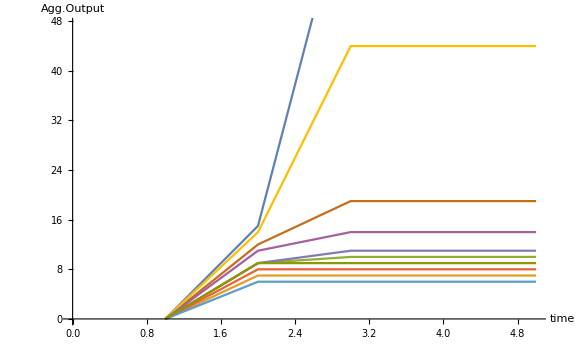

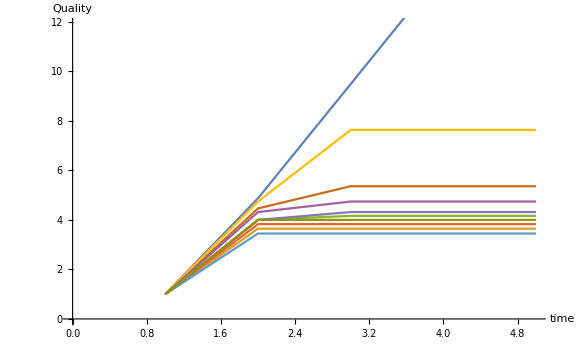

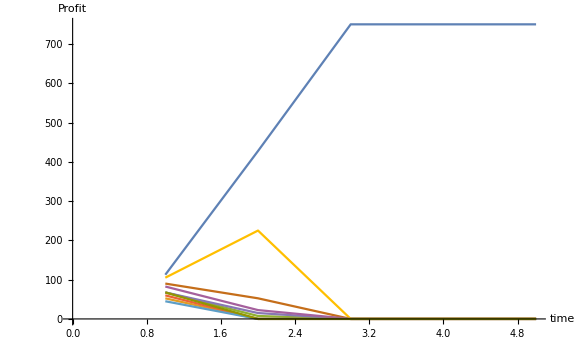

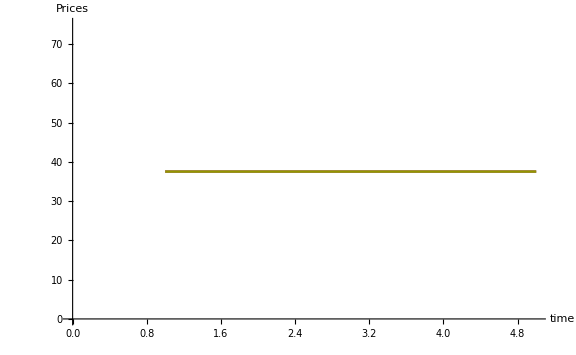

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*Batch Runs*)
(*------------------------------------------------------------------------------------------------------------------------------*)

R=20;
T = 5; (*100*)
count = 0;

Do[
count = count + 1;
(*Store Results in Lists such that 
e.g. priceList[[1,2]] gives the price of the second firm in period 1!!*)

(*prices*)
priceList =Table[Table[0.0,{i,1,n}],{i,1,T}];
qualityList =Table[Table[0.0,{i,1,n}],{i,1,T}];
(*Quantities produced*)
quantPeriod =Table[Table[0.0,{i,1,n}],{i,1,T}];
quantAgg=Table[Table[0.0,{i,1,n}],{i,1,T}]; (*aggregated output*)
(*Profits*)
profitList =Table[Table[0.0,{i,1,n}],{i,1,T}];
(*List of probabilities*)
probList =Table[Table[0.0,{i,1,n}],{i,1,T}];

(*PERIODS*)
Do[
(*compute prices*)
priceList[[t]] =Table[pFirmSelf[cSelf[cp,cs],eta],{i,1,n}];
(*compute aggregated output: depends on aggregate output and period output of LAST PERIOD*)
If[t==1,
quantAgg[[t]]=Table[0.0,{i,1,n}],
quantAgg[[t]]=Table[quantAgg[[t-1,i]]+ quantPeriod[[t-1,i]],{i,1,n}]];
(*compute quality using aggregated output*)
qualityList[[t]] =Table[qualityFirm[uBar, alpha, beta,quantAgg[[t,i]]],{i,1,n}];
(*Compute the probabilities and append them to a list! 
Since each consumer computes these probabilities the same way 
it is necessary to compute them for only one consumer*)
probList[[t]] = Table[probability[i,priceList[[t]], qualityList[[t]]],{i,1,n}];
(*compute demand*)
choiceListAll = RandomChoice[probList[[t]] ->Id,m];
(*Compute quantities produced in period t*)
quantPeriod[[t]] = Table[Count[choiceListAll,i],{i,1,n}];
(*compute profits*)
profitList[[t]] =Table[profit[quantPeriod[[t,i]],priceList[[t,i]],cSelf[cp,cs]],{i,1,n}],

{t,1,T}
];
,{r,1,R}]

(*------------------------------------------------------------------------------------------------------------------------------*)
(*Results*)
(*------------------------------------------------------------------------------------------------------------------------------*)
Print["Period Quantities: ", TableForm[quantPeriod]]
Print["Prices: ",TableForm[priceList]]
Print["Qualities: ",TableForm[qualityList]]
Print["Agg. Quantities: ",TableForm[quantAgg]]
Print["Profits: ",TableForm[profitList]]
Print["Probs: ",TableForm[probList]]

ListPlot[Table[Table[quantAgg[[t,j]],{t,1,5}],{j,1,n}],Joined->True, ImageSize->Large,AxesLabel->{HoldForm[time],HoldForm[Agg.Output]}]
ListPlot[Table[Table[qualityList[[t,j]],{t,1,5}],{j,1,n}],Joined->True, ImageSize->Large,AxesLabel->{HoldForm[time],HoldForm[Quality]}]
ListPlot[Table[Table[profitList[[t,j]],{t,1,5}],{j,1,n}],Joined->True,PlotRange->All, ImageSize->Large,AxesLabel->{HoldForm[time],HoldForm[Profit]}]
ListPlot[Table[Table[priceList[[t,j]],{t,1,5}],{j,1,n}],Joined->True, ImageSize->Large,AxesLabel->{HoldForm[time],HoldForm[Prices]}]
```

```mathematica
(*count*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------ EXERCISE 1 c) -------------------------------------------------------------*)
(*---------------------------------(*FIXED STRATEGIES: FIRMS BUY SMART COMPONENT*)-----------------------------------------*)
```

Period Quantities: 11 | 15 | 4 | 7 | 12 | 11 | 10 | 7 | 8 | 15
8 | 8 | 15 | 8 | 10 | 11 | 12 | 9 | 7 | 12
11 | 3 | 8 | 10 | 13 | 9 | 11 | 9 | 9 | 17
7 | 10 | 17 | 5 | 11 | 7 | 14 | 11 | 11 | 7
10 | 6 | 13 | 8 | 11 | 12 | 9 | 8 | 16 | 7

Prices: 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
40.625 | 40.625 | 40.625 | 40.625 | 40.625 | 40.625 | 40.625 | 40.625 | 40.625 | 40.625
42.1875 | 42.1875 | 42.1875 | 42.1875 | 42.1875 | 42.1875 | 42.1875 | 42.1875 | 42.1875 | 42.1875
42.9688 | 42.9688 | 42.9688 | 42.9688 | 42.9688 | 42.9688 | 42.9688 | 42.9688 | 42.9688 | 42.9688
43.3594 | 43.3594 | 43.3594 | 43.3594 | 43.3594 | 43.3594 | 43.3594 | 43.3594 | 43.3594 | 43.3594

Market Share: 1
1
1
1
1

Profit Firms: 82.5 | 112.5 | 30. | 52.5 | 90. | 82.5 | 75. | 52.5 | 60. | 112.5
85. | 85. | 159.375 | 85. | 106.25 | 116.875 | 127.5 | 95.625 | 74.375 | 127.5
134.063 | 36.5625 | 97.5 | 121.875 | 158.438 | 109.688 | 134.063 | 109.688 | 109.688 | 207.188
90.7813 | 129.688 | 220.469 | 64.8438 | 142.656 | 90.7813 | 181.563 | 142.656 | 142.656 | 90.7813
133.594 | 80.1563 | 173.672 | 106.875 | 146.953 | 160.313 | 120.234 | 106.875 | 213.75 | 93.5156

Profit Specialist: 0.
250.
375.
437.5
468.75

Agg. Quantities: 0.
100.
200.
300.
400.

Probs: 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1

Quality: 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
11. | 11. | 11. | 11. | 11. | 11. | 11. | 11. | 11. | 11.
15.1421 | 15.1421 | 15.1421 | 15.1421 | 15.1421 | 15.1421 | 15.1421 | 15.1421 | 15.1421 | 15.1421
18.3205 | 18.3205 | 18.3205 | 18.3205 | 18.3205 | 18.3205 | 18.3205 | 18.3205 | 18.3205 | 18.3205
21. | 21. | 21. | 21. | 21. | 21. | 21. | 21. | 21. | 21.

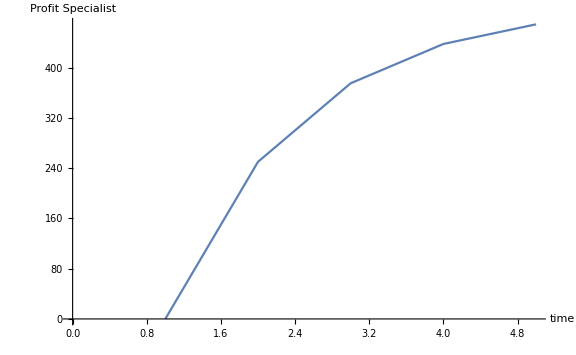

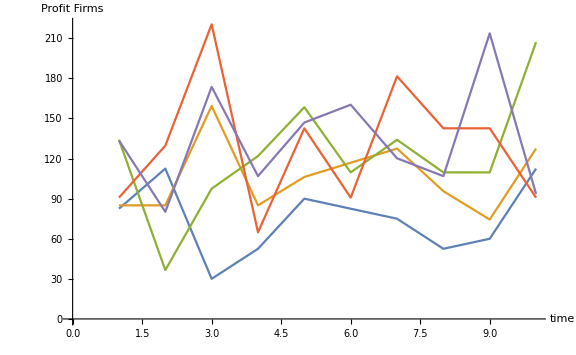

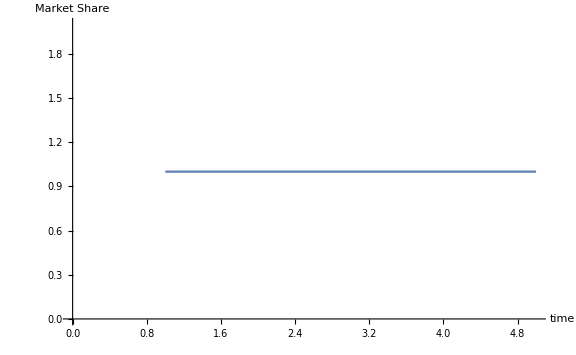

```mathematica
T=5;
R=20;
count=0;
Do[
count=count+1;
(*prices*)
priceSpec =Table[0.0,{i,1,T}];
priceListFirm=Table[Table[0.0,{i,1,n}],{i,1,T}];
(*qualities*)
qualitySpec =Table[0.0,{i,1,T}];
qualityListFirm =Table[Table[0.0,{i,1,n}],{i,1,T}];
(*quantities produced*)
quantPeriodFirm =Table[Table[0.0,{i,1,n}],{i,1,T}];
quantPeriodSpec =Table[0.0,{i,1,T}];
quantAggFirm=Table[Table[0.0,{i,1,n}],{i,1,T}]; (*aggregated output of firm*)
quantAggSpec =Table[0.0,{i,1,T}];(*aggregated output of specialist*)
(*market share of specialist*)
msSpec= Table[0.0,{i,1,T}];
(*markup of specialist*)
markupSpec =Table[0.0,{i,1,T}];
(*profits*)
profitListFirm =Table[Table[0.0,{i,1,n}],{i,1,T}];
profitSpec = Table[0.0,{i,1,T}];
(*list of probabilities*)
probList =Table[Table[0.0,{i,1,n}],{i,1,T}];

(*PERIODS*)
Do[
(*compute markup*)
If[t==1,
markupSpec[[t]]=0.0,
markupSpec[[t]] = etaSpec[delta, markupSpec[[t-1]], msSpec[[t-1]], etaBar];
];
(*compute price of specialist*)
priceSpec[[t]]=pSpec[cs,markupSpec[[t]]];
(*compute prices of firms*)
priceListFirm[[t]] =Table[pFirmSpec[cSpec[cp,cs, markupSpec[[t]]],eta],{i,1,n}];
(*compute aggregated output of specialist: depends on aggregate output and period output of LAST PERIOD*)
If[t==1,
quantAggSpec[[t]]=0.0,
quantAggSpec[[t]]=quantAggSpec[[t-1]]+ quantPeriodSpec[[t-1]]];
(*compute quality using aggregated output*)
qualitySpec[[t]] =uBar*(1+ beta*quantAggSpec[[t]]^alpha);
qualityListFirm[[t]] =Table[qualitySpec[[t]],{i,1,n}];
(*Compute the probabilities and append them to a list! 
Since each consumer computes these probabilities the same way 
it is necessary to compute them for only one consumer*)
probList[[t]] = Table[probability[i,priceListFirm[[t]], qualityListFirm[[t]]],{i,1,n}];
(*compute demand*)
choiceListAll = RandomChoice[probList[[t]] ->Id,m];
(*compute quantities produced by firms in period t*)
quantPeriodFirm[[t]] = Table[Count[choiceListAll,i],{i,1,n}];
(*compute quantities produced by specialist in period t*)
quantPeriodSpec[[t]] =Sum[quantPeriodFirm[[t,i]],{i,1,n}];
(*compute market share*)
msSpec[[t]]=ms[t,n,quantPeriodSpec[[t]], quantPeriodFirm];
(*compute profits*)
profitListFirm[[t]] =Table[profit[quantPeriodFirm[[t,i]],priceListFirm[[t,i]],cSelf[cp,cs]],{i,1,n}];
profitSpec[[t]]=profit[quantPeriodSpec[[t]],priceSpec[[t]],cs],
{t,1,T}
];
,{r,1,R}];

Print["Period Quantities: ", TableForm[quantPeriodFirm]]
Print["Prices: ",TableForm[priceListFirm]]
Print["Market Share: ",TableForm[msSpec]]
Print["Profit Firms: ",TableForm[profitListFirm]]
Print["Profit Specialist: ",TableForm[profitSpec]]
Print["Agg. Quantities: ",TableForm[quantAggSpec]]
Print["Probs: ",TableForm[probList]]
Print["Quality: ",TableForm[qualityListFirm]]

(*ListPlot[Table[Table[quantAgg[[t,j]],{t,1,5}],{j,1,n}],Joined->True, ImageSize->Large,AxesLabel->{HoldForm[time],HoldForm[Agg.Output]}]
ListPlot[Table[Table[qualityList[[t,j]],{t,1,5}],{j,1,n}],Joined->True, ImageSize->Large,AxesLabel->{HoldForm[time],HoldForm[Quality]}]
ListPlot[Table[Table[profitList[[t,j]],{t,1,5}],{j,1,n}],Joined->True,PlotRange->All, ImageSize->Large,AxesLabel->{HoldForm[time],HoldForm[Profit]}]
ListPlot[Table[Table[priceList[[t,j]],{t,1,5}],{j,1,n}],Joined->True, ImageSize->Large,AxesLabel->{HoldForm[time],HoldForm[Prices]}]*)

ListPlot[profitSpec,Joined->True, ImageSize->Large,AxesLabel->{HoldForm[time],HoldForm[Profit Specialist]}]
ListPlot[profitListFirm,Joined->True,PlotRange->All, ImageSize->Large,AxesLabel->{HoldForm[time],HoldForm[Profit Firms]}]
ListPlot[msSpec,Joined->True, ImageSize->Large,AxesLabel->{HoldForm[time],HoldForm[Market Share]}]
```

```mathematica
count
```

20